```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_All.txt","Table"];
```

```mathematica
{totalnum} = Dimensions[rawdata];
```

```mathematica
Clear[k]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,totalnum}]
```

```mathematica
k=1;
z=0;
While[(k+z)<totalnum,If[Dimensions[Dimensions[Take[rawdata,k]]]=={2},k++,{rawdata=Drop[rawdata,{k}],z++}]]
```

```mathematica
Dimensions[rawdata]
```

{59540,3}

```mathematica
num=Dimensions[rawdata][[1]]
```

59540

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(.0578*Log[voltage[[i]]]^8+.4845*Log[voltage[[i]]]^7+1.593*Log[voltage[[i]]]^6+2.521*Log[voltage[[i]]]^5+1.813*Log[voltage[[i]]]^4+.2846*Log[voltage[[i]]]^3-.1635*Log[voltage[[i]]]^2-.3503Log[voltage[[i]]]+.6568),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{i,temp[[i]]},2],{i,1,num}]
```

```mathematica
temp;
```

```mathematica
voltage;
```

```mathematica
num
```

59540

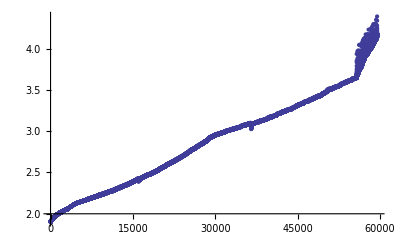

```mathematica
ListPlot[timetemp]
```

```mathematica
ListPlot[timetemp]
```

-Graphics-

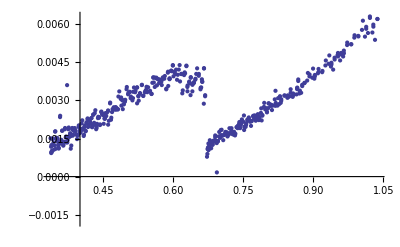

```mathematica
threshold=.0008;
threshold2=.002;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,6,6977-7}]
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold2,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-10,i}]][[1]]-Mean[Take[voltage,{i+50,i+80}]][[1]]}}]}],{i,6977,num-80}]
ListPlot[dT]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

```mathematica
Dimensions[dT]
```

{501,2}

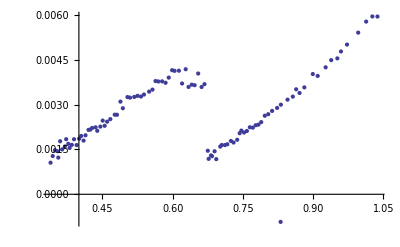

```mathematica
avgsize=5;
avgnum=Quotient[501,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT]
```

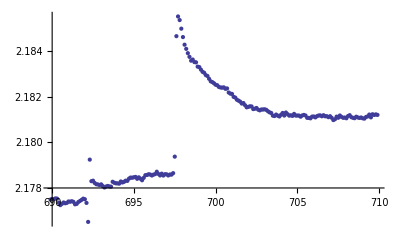

```mathematica
ListPlot[Take[timetemp,{6900,7100}]]
```

```mathematica
num
```

59540

```mathematica
Q=10.5^2/1116 10^-2;
```

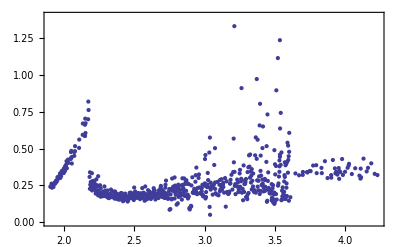

```mathematica
threshold=.002;
threshold2=.001;
threshold3=.002;
threshold4=.005;
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-5,i}]][[1]]+Mean[Take[temp,{i+3,i+7}]][[1]])}}]}],{i,6,6977-7}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+80}]][[1]])}}]}],{i,6977,30000}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold3,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+80}]][[1]])}}]}],{i,30001,54500}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold4,{dT=Join[dT,{{temp[[i]][[1]],Q*10/(-Mean[Take[temp,{i-10,i-3}]][[1]]+Mean[Take[temp,{i+30,i+50}]][[1]])}}]}],{i,55000,num-100}]

ListPlot[dT,PlotRange->{0,1.4},Frame->True]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

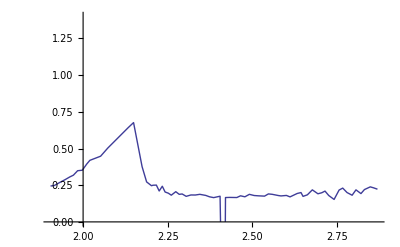

```mathematica
avgsize=5;
avgnum=Quotient[355,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT,PlotRange->{0,1.4},Joined->True]
```

```mathematica
avgdT;
```

```mathematica
avgnum
```

71

```mathematica
Dimensions[dT]
```

{355,2}

```mathematica
avgdT
```

{{1.90375,0.244584},{1.91452,0.247487},{1.93131,0.269129},{1.94754,0.288917},{1.96094,0.306774},{1.97129,0.318329},{1.98382,0.348745},{1.99777,0.352367},{2.0104,0.393265},{2.01997,0.419468},{2.05179,0.447705},{2.07279,0.502739},{2.13364,0.643049},{2.14915,0.676689},{2.17435,0.376592},{2.18774,0.272496},{2.20214,0.246586},{2.20669,0.24991},{2.21657,0.250763},{2.22492,0.210629},{2.23413,0.243024},{2.2424,0.203732},{2.25184,0.195651},{2.26071,0.182093},{2.27394,0.205878},{2.28408,0.18789},{2.29282,0.190266},{2.30472,0.174195},{2.31872,0.183537},{2.33168,0.183159},{2.34503,0.187877},{2.36262,0.180401},{2.37351,0.171141},{2.38593,0.165438},{2.40487,0.174997},{2.41667,-1.33892},{2.4209,0.165979},{2.4328,0.166835},{2.45433,0.16606},{2.46543,0.177815},{2.47823,0.171043},{2.49152,0.187775},{2.50561,0.17977},{2.51814,0.177678},{2.53632,0.175603},{2.54779,0.190609},{2.55884,0.188031},{2.57759,0.179458},{2.58505,0.176983},{2.60091,0.18029},{2.6117,0.170471},{2.63289,0.193685},{2.64407,0.199874},{2.65015,0.173908},{2.66297,0.184529},{2.67757,0.218361},{2.69416,0.191549},{2.70566,0.198733},{2.7151,0.2099},{2.72612,0.179796},{2.74194,0.153084},{2.75669,0.216986},{2.76745,0.230342},{2.7802,0.200028},{2.79522,0.18172},{2.80661,0.218383},{2.82134,0.192953},{2.83164,0.220368},{2.84893,0.238736},{2.85836,0.232345},{2.87013,0.222886}}

```mathematica
Dimensions[avgdT]
```

{71,2}

```mathematica
normavgdT=Table[0,{i,71}];
```

```mathematica
Do[normavgdT[[i]]={Take[avgdT[[i]],{1}][[1]],Take[avgdT[[i]],{2}][[1]]-(0.015932467940417003*Take[avgdT[[i]],{1}][[1]]+0.0012545580454563976*(Take[avgdT[[i]],{1}][[1]])^3)},{i,1,71}]
```

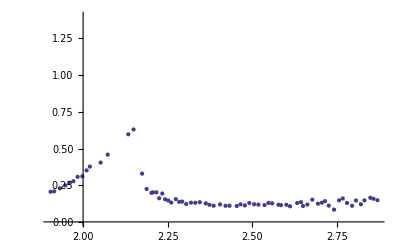

```mathematica
ListPlot[normavgdT,PlotRange->{0,1.4}]
```

```mathematica
Take[avgdT[[1]],{2}][[1]]
```

0.244584

```mathematica
finalC=Table[1,{i,71}];
Do[finalC[[i]]={normavgdT[[i]][[1]],(1/25.4)/(.0005385)normavgdT[[i]][[2]]},{i,1,71}]
```

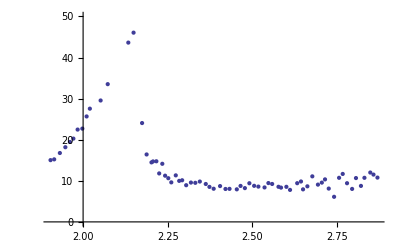

$Aborted

```mathematica
ListPlot[finalC,PlotRange->{0,50}]
```